```mathematica
ClearAll["Global`*"]
```

```mathematica
(* set your home directory *)
SetDirectory[NotebookDirectory[]];
```

# CATS’ PDEs Logo

## Mesh

```mathematica
nodes=Import["nodes.dat","Table"];
triangles=Import["triangles.dat","Table"]+1;
𝒦=MeshRegion[nodes,Triangle/@triangles];
```

```mathematica
DirichletNodes=Import["DirichletNodes.dat","List"]+1;
HighlightMesh[𝒦,None,MeshCellHighlight->{{0,DirichletNodes}->Red}]
```

-Graphics-

## Plotting

```mathematica
ξ=Import["xi.dat","List"];
```

```mathematica
Subscript[u, h]=Interpolation[Table[{nodes[[i]],ξ[[i]]},{i,Length@nodes}],InterpolationOrder->1];
```

```mathematica
Plot3D[Subscript[u, h][x,y],{x,y}∈𝒦,Mesh->All,PlotRange->All]
```

-Graphics3D-

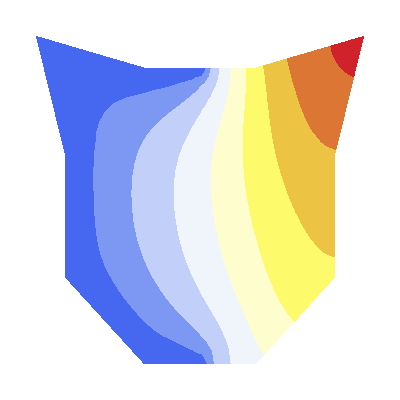

```mathematica
𝒯=ContourPlot[Subscript[u, h][x,y],{x,y}∈𝒦,PlotRange->All,Frame->False,ColorFunction->"TemperatureMap",ContourStyle->None]
```

```mathematica
nodesLogo=Import["../Generate Mesh/nodesLogo.dat","Table"];
fullMesh=MeshRegion[nodesLogo,Triangle/@Import["../Generate Mesh/trianglesLogo.dat","Table"],
MeshCellStyle->{{2,All}->Opacity[.1,Black],{1,All}->{Black,Thickness@.008},{0,All}->Directive[PointSize@0.02,Black]}];
faceMesh=MeshRegion[nodesLogo,Line/@{{11,12},{12,13},{13,14},{12,15},{15,16},{17,18},{18,19},{20,21},{21,22}},MeshCellStyle->{{0,All}->Directive[PointSize@0.03,Black],{1,All}->{Black,Thickness@0.02}}];
```

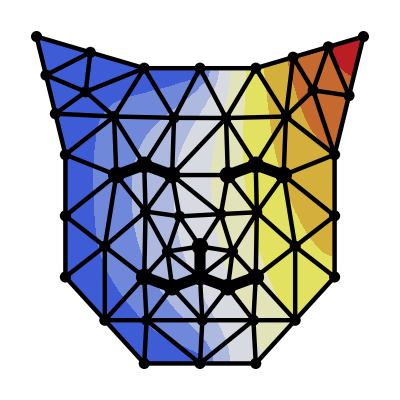

```mathematica
Show[𝒯,HighlightMesh[fullMesh,None,PlotTheme->"Lines"],faceMesh]
```